## Turing Machines

### (1,2)

```mathematica
hist12=ParallelMap[#->IteratedGame[Function[rule,TuringMachineStrategy[rule]]/@#,{},200]&,Tuples[{#,1,2}&/@Range[0,TMMaxIndex[1,2]],2]];
```

```mathematica
selectedhist=SelectedTuringMachines[hist12];
```

```mathematica
good=Keys[selectedhist]
```

{{{1,1,2},{1,1,2}},{{1,1,2},{3,1,2}},{{1,1,2},{5,1,2}},{{1,1,2},{7,1,2}},{{1,1,2},{13,1,2}},{{1,1,2},{15,1,2}},{{3,1,2},{1,1,2}},{{3,1,2},{3,1,2}},{{3,1,2},{5,1,2}},{{3,1,2},{7,1,2}},{{3,1,2},{13,1,2}},{{3,1,2},{15,1,2}},{{5,1,2},{1,1,2}},{{5,1,2},{3,1,2}},{{5,1,2},{5,1,2}},{{5,1,2},{7,1,2}},{{5,1,2},{13,1,2}},{{5,1,2},{15,1,2}},{{7,1,2},{1,1,2}},{{7,1,2},{3,1,2}},{{7,1,2},{5,1,2}},{{7,1,2},{7,1,2}},{{7,1,2},{13,1,2}},{{7,1,2},{15,1,2}},{{13,1,2},{1,1,2}},{{13,1,2},{3,1,2}},{{13,1,2},{5,1,2}},{{13,1,2},{7,1,2}},{{13,1,2},{13,1,2}},{{13,1,2},{15,1,2}},{{15,1,2},{1,1,2}},{{15,1,2},{3,1,2}},{{15,1,2},{5,1,2}},{{15,1,2},{7,1,2}},{{15,1,2},{13,1,2}},{{15,1,2},{15,1,2}}}

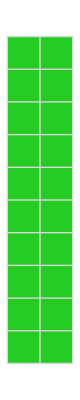
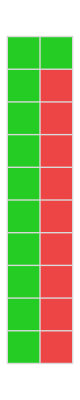
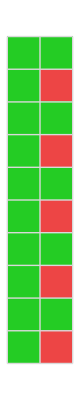
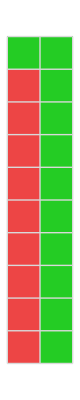
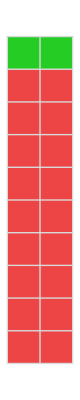
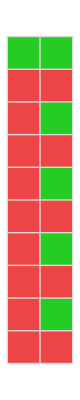
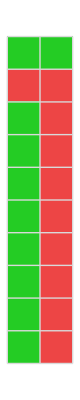
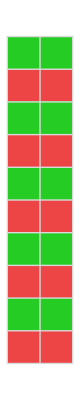
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
IteratedGamePlot[TuringMachineStrategy[#]&/@#]&/@good
```

#### Prisoner’s Dilemma

```mathematica
tb12pdl=TournamentScoreboard[{"TM","TM"},TournamentScores[PerspectiveBuilders[TuringMachineStrategy,1,2], Tuples[Range[0,TMMaxIndex[1,2]],2], $PrisonersDilemma, 200],"SortKey"->"TotalPayoff"]
```

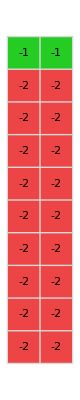
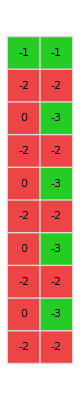
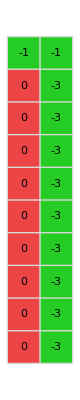
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Function[m,Labeled[IteratedGamePlot[{TuringMachineStrategy[{3,1,2}],TuringMachineStrategy[{m,1,2}]},{},10,$PrisonersDilemma,"ShowLabels"->True],{3,m},Top]]/@Rest[Normal[#ID&/@tb12pdl]]
```

Machine plot

```mathematica
Grid[{Grid[Join[{{Style[3,16,Bold],Style[#,16,Bold]}},TMMoveSequencePlot[{{3,1,2},{#,1,2}},{},6]]]&/@Rest[Normal[#ID&/@tb12pdl]]},Dividers->All]
```

3 | 15
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics- | 3 | 7
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics- | 3 | 13
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics- | 3 | 1
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics- | 3 | 5
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

#### Matching Pennies

```mathematica
tb12mp=TournamentScoreboard[{"TM","TM"},TournamentScores[PerspectiveBuilders[TuringMachineStrategy,1,2], Tuples[Range[0,TMMaxIndex[1,2]],2], $MatchingPennies, 200],"SortKey"->"TotalPayoff"]
```

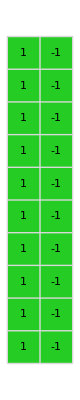
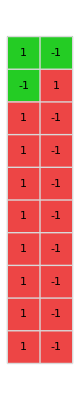
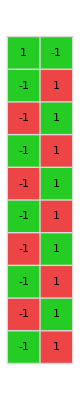
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Function[m,Labeled[IteratedGamePlot[{TuringMachineStrategy[{13,1,2}],TuringMachineStrategy[{m,1,2}]},{},10,$MatchingPennies,"ShowLabels"->True],{13,m},Top]]/@Rest[Normal[#ID&/@tb12mp]]
```

Machine plot(# vs 13)

```mathematica
Grid[{Grid[Join[{{Style[#,16,Bold],Style[13,16,Bold]}},TMMoveSequencePlot[{{#,1,2},{13,1,2}},{},7]]]&/@Rest[Normal[#ID&/@tb12mp]]},Dividers->All]
```

1 | 13
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics- | 5 | 13
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics- | 3 | 13
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics- | 15 | 13
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics- | 7 | 13
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

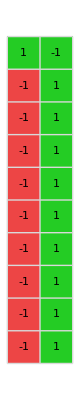
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Function[m,Labeled[IteratedGamePlot[{TuringMachineStrategy[{m,1,2}],TuringMachineStrategy[{13,1,2}]},{},10,$MatchingPennies,"ShowLabels"->True],{m,13},Top]]/@Rest[Normal[#ID&/@tb12mp]]
```

Machine plot(13 vs #)

```mathematica
Grid[{Grid[Join[{{Style[13,16,Bold],Style[#,16,Bold]}},TMMoveSequencePlot[{{13,1,2},{#,1,2}},{},7]]]&/@Rest[Normal[#ID&/@tb12mp]]},Dividers->All]
```

13 | 1
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics- | 13 | 5
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics- | 13 | 3
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics- | 13 | 15
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics- | 13 | 7
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

### (2, 2)

```mathematica
pairs22=Tuples[{#,2,2}&/@Range[0,TMMaxIndex[2,2]],2];
```

```mathematica
Length[pairs22]
```

16777216

```mathematica
hist22=ParallelMap[#->IteratedGame[Function[rule,TuringMachineStrategy[rule]]/@#,{},10]&,pairs22];
```